# Defining our objects separately:

```mathematica
cDiffMat[m_]:=SparseArray[{Band[{1,2}]->1,Band[{2,1}]->-1,Band[{1,m}]->-1,Band[{m,1}]->1},{m,m}]
```

```mathematica
idPluscDiffMat[m_]:=IdentityMatrix[m]+ν cDiffMat[m]
```

```mathematica
inverse[m_]:=Inverse@idPluscDiffMat[m]
```

```mathematica
det[m_]:=Det@idPluscDiffMat[m]
```

```mathematica
idPluscDiffMat[8]//MatrixForm
```

(1 | ν | 0 | 0 | 0 | 0 | 0 | -ν
-ν | 1 | ν | 0 | 0 | 0 | 0 | 0
0 | -ν | 1 | ν | 0 | 0 | 0 | 0
0 | 0 | -ν | 1 | ν | 0 | 0 | 0
0 | 0 | 0 | -ν | 1 | ν | 0 | 0
0 | 0 | 0 | 0 | -ν | 1 | ν | 0
0 | 0 | 0 | 0 | 0 | -ν | 1 | ν
ν | 0 | 0 | 0 | 0 | 0 | -ν | 1)

# First claim: for even matrix sizes, the element inverse_(1,2)=-inverse_(1,last). Proof.

### From the definition of the inverse matrix, inverse_(1,2) is obtained by deleting its first column and second row and taking det and flipping the sign, while inverse_(1,m) is obtained by deleting the first column and last row and taking det and multiplying by (-1)^(m+1):

### Example with an 8x8 original matrix:

```mathematica
{-Det[({{ν, 0, 0, 0, 0, 0, -ν}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}})],(-1)^(8+1)Det[({{ν, 0, 0, 0, 0, 0, -ν}, {1, ν, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}})]}//Expand
```

{-ν-5 ν^3-6 ν^5,ν+5 ν^3+6 ν^5}

```mathematica
inverse[8]
```

{{(1+6 ν^2+10 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν-5 ν^3-6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν^3-2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(2 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^3+2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν+5 ν^3+6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6)},{(ν+5 ν^3+6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(1+6 ν^2+10 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν-5 ν^3-6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν^3-2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(2 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^3+2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6)},{(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν+5 ν^3+6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(1+6 ν^2+10 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν-5 ν^3-6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν^3-2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(2 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^3+2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6)},{(ν^3+2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν+5 ν^3+6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(1+6 ν^2+10 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν-5 ν^3-6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν^3-2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(2 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6)},{(2 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^3+2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν+5 ν^3+6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(1+6 ν^2+10 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν-5 ν^3-6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν^3-2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6)},{(-ν^3-2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(2 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^3+2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν+5 ν^3+6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(1+6 ν^2+10 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν-5 ν^3-6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6)},{(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν^3-2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(2 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^3+2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν+5 ν^3+6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(1+6 ν^2+10 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν-5 ν^3-6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6)},{(-ν-5 ν^3-6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(-ν^3-2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(2 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^3+2 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(ν^2+4 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6),(ν+5 ν^3+6 ν^5)/(1+8 ν^2+20 ν^4+16 ν^6),(1+6 ν^2+10 ν^4+4 ν^6)/(1+8 ν^2+20 ν^4+16 ν^6)}}

Expand the element inverse_(1,2) along the first row to get a tridiagonal circulant and an upper triangular matrix:

```mathematica
-Det[({{ν, 0, 0, 0, 0, 0, -ν}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}})]==-ν Det[({{1, ν, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0}, {0, -ν, 1, ν, 0, 0}, {0, 0, -ν, 1, ν, 0}, {0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, -ν, 1}})]-(-1)^(m-1)ν Det[({{-ν, 1, ν, 0, 0, 0}, {0, -ν, 1, ν, 0, 0}, {0, 0, -ν, 1, ν, 0}, {0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, -ν, 1}, {0, 0, 0, 0, 0, -ν}})]//Expand
```

```mathematica
-ν-5 ν^3-6 ν^5==-ν-5 ν^3-6 ν^5-ν^7+(-1)^m ν^7/.m->8
```

True

Expand the element inverse_(1,m) along the first row to get a lower triangular and a tridiagonal circulant matrix:

```mathematica
(-1)^(m+1)Det[({{ν, 0, 0, 0, 0, 0, -ν}, {1, ν, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}})]==(-1)^(m+1)ν Det[({{ν, 0, 0, 0, 0, 0}, {1, ν, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0}, {0, -ν, 1, ν, 0, 0}, {0, 0, -ν, 1, ν, 0}, {0, 0, 0, -ν, 1, ν}})]-(-1)^(m-1)ν Det[({{1, ν, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0}, {0, -ν, 1, ν, 0, 0}, {0, 0, -ν, 1, ν, 0}, {0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, -ν, 1}})]//Expand
```

```mathematica
-(-1)^(1+m) ν-5 (-1)^(1+m) ν^3-6 (-1)^(1+m) ν^5==(-1)^m ν+5 (-1)^m ν^3+6 (-1)^m ν^5+(-1)^m ν^7+(-1)^(1+m) ν^7/.m->8
```

True

### From this we see that if m is even, the two expressions are the negative of each other. So from now on we can and will assume that the matrix size is odd.

# Lemma.

Recurrence for this tridiag circulant matrix (1 | ν | 0 | 0 | 0 | 0 | 0 | 0
-ν | 1 | ν | 0 | 0 | 0 | 0 | 0
0 | -ν | 1 | ν | 0 | 0 | 0 | 0
0 | 0 | -ν | 1 | ν | 0 | 0 | 0
0 | 0 | 0 | -ν | 1 | ν | 0 | 0
0 | 0 | 0 | 0 | -ν | 1 | ν | 0
0 | 0 | 0 | 0 | 0 | -ν | 1 | ν
0 | 0 | 0 | 0 | 0 | 0 | -ν | 1): by expanding along the first row we get

```mathematica
Det@({{1, ν, 0, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, 0, -ν, 1}})==Det@({{1, ν, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}})+ν Det@({{ν, 0, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}})==Det@({{1, ν, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}})+ν^2 Det@({{1, ν, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0}, {0, -ν, 1, ν, 0, 0}, {0, 0, -ν, 1, ν, 0}, {0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, -ν, 1}})//Expand
```

True

```mathematica
RSolve[{tridiag[n+2]==tridiag[n+1]+ν^2 tridiag[n],tridiag[1]==1,tridiag[2]==1+ν^2},tridiag[n],n]
```

{{tridiag[n]→(2^(-1-n) (-(1-√(1+4 ν^2))^n+√(1+4 ν^2) (1-√(1+4 ν^2))^n+(1+√(1+4 ν^2))^n+√(1+4 ν^2) (1+√(1+4 ν^2))^n))/(√(1+4 ν^2))}}

```mathematica
FullSimplify[(2^(-1-n) (-(1-√(1+4 ν^2))^n+√(1+4 ν^2) (1-√(1+4 ν^2))^n+(1+√(1+4 ν^2))^n+√(1+4 ν^2) (1+√(1+4 ν^2))^n))/(√(1+4 ν^2))]
```

```mathematica
(2^(-1-n) ((1+√(1+4 ν^2))^(1+n)-(1-√(1+4 ν^2))^(n+1) ))/(√(1+4 ν^2))==(2^(-1-n) (-(1-√(1+4 ν^2))^n+√(1+4 ν^2) (1-√(1+4 ν^2))^n+(1+√(1+4 ν^2))^n+√(1+4 ν^2) (1+√(1+4 ν^2))^n))/(√(1+4 ν^2))//Simplify
```

True

#### In explicit form for matrix size n x n:

```mathematica
((1+√(1+4 ν^2))^(1+n)-(1-√(1+4 ν^2))^(n+1))/(2^(n+1)√(1+4 ν^2))
```

```mathematica
((1+√(1+4 ν^2))^(1+n)-(1-√(1+4 ν^2))^(n+1))/(2^(n+1)√(1+4 ν^2))/.n->{1,2,3}//Simplify
```

{1,1+ν^2,1+2 ν^2}

### So the Lemma is proved. In particular, these tridiag determinants are always positive.

# Second claim: explicit form for the element inverse_(1,2) for odd matrix sizes

```mathematica
idPluscDiffMat[11]//MatrixForm
```

```mathematica
({{1, ν, 0, 0, 0, 0, 0, 0, 0, 0, -ν}, {-ν, 1, ν, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -ν, 1, ν}, {ν, 0, 0, 0, 0, 0, 0, 0, 0, -ν, 1}})
```

We expand the LHS along its first row to get a tridiagonal circulant matrix and an upper triangular matrix:

```mathematica
(-1)^(1+2)Det@({{ν, 0, 0, 0, 0, 0, 0, 0, 0, -ν}, {-ν, 1, ν, 0, 0, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, 0, 0, 0, -ν, 1}})==-ν Det@({{1, ν, 0, 0, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, 0, 0, -ν, 1}})-ν Det@({{-ν, 1, ν, 0, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, 0, 0, -ν, 1}, {0, 0, 0, 0, 0, 0, 0, 0, -ν}})//Expand
```

True

```mathematica
ν^(n-1)-ν((1+√(1+4 ν^2))^(n-1)- (1-√(1+4 ν^2))^(n-1))/(2^(n-1)√(1+4 ν^2))/.n->11//Expand
```

-ν-8 ν^3-21 ν^5-20 ν^7-5 ν^9+ν^10

So the “numerator” of inverse_(1,2) for size n x n (n odd) is ν^(n-1)-ν((1+√(1+4 ν^2))^(n-1)- (1-√(1+4 ν^2))^(n-1))/(2^(n-1)√(1+4 ν^2)). From here we should proceed as in the other notebook.

```mathematica
Table[{det[n] inverse[n][[1,2]],-ν((1+√(1+4 ν^2))^(n-1)-(1-√(1+4 ν^2))^(n-1))/(2^(n-1)√(1+4 ν^2))+ν^(n-1)//Expand},{n,3,10}]
```

{{-ν+ν^2,-ν+ν^2},{-ν,-ν},{-ν-2 ν^3+ν^4,-ν-2 ν^3+ν^4},{-ν-3 ν^3,-ν-3 ν^3},{-ν-4 ν^3-3 ν^5+ν^6,-ν-4 ν^3-3 ν^5+ν^6},{-ν-5 ν^3-6 ν^5,-ν-5 ν^3-6 ν^5},{-ν-6 ν^3-10 ν^5-4 ν^7+ν^8,-ν-6 ν^3-10 ν^5-4 ν^7+ν^8},{-ν-7 ν^3-15 ν^5-10 ν^7,-ν-7 ν^3-15 ν^5-10 ν^7}}

```mathematica
Table[{det[n] inverse[n][[1,2]]==-ν((1+√(1+4 ν^2))^(n-1)-(1-√(1+4 ν^2))^(n-1))/(2^(n-1)√(1+4 ν^2))+ν^(n-1)//Expand},{n,3,10}]
```

{{True},{True},{True},{True},{True},{True},{True},{True}}

# Claim 2.5: explicit form for the element inverse_(1,1): it is by definition a tridiagonal matrix for which we have an explicit form: ((1+√(1+4 ν^2))^(1+n)-(1-√(1+4 ν^2))^(n+1))/(2^(n+1)√(1+4 ν^2)), we just need an index shift, because the original matrix is n x n, and we need to take a minor of size (n-1)x (n-1). So the lower left element of the inverse (multiplied by the det) is ((1+√(1+4 ν^2))^n-(1-√(1+4 ν^2))^n)/(2^n √(1+4 ν^2)).

```mathematica
Det@({{1, ν, 0, 0, 0, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, 0, 0, 0, -ν, 1}})
```

1+9 ν^2+28 ν^4+35 ν^6+15 ν^8+ν^10

```mathematica
det[11] inverse[11][[1,1]]
```

1+9 ν^2+28 ν^4+35 ν^6+15 ν^8+ν^10

```mathematica
(2^(-1-n) (-(1-√(1+4 ν^2))^(1+n)+(1+√(1+4 ν^2))^(1+n)))/(√(1+4 ν^2))/.n->10//Expand
```

1+9 ν^2+28 ν^4+35 ν^6+15 ν^8+ν^10

# Claim 2.75: For odd n, the k^th element (1≤k≤n) of the 1^st row of the inverse matrix multiplied by det[original matrix] is ((1+√(1+4 ν^2))^(k-1)-(1-√(1+4 ν^2))^(k-1))/(2^(k-1)√(1+4 ν^2)) ν^(n-k+1)+(-1)^(k-1)ν^(k-1)((1+√(1+4 ν^2))^(n-k+1)-(1-√(1+4 ν^2))^(n-k+1))/(2^(n-k+1)√(1+4 ν^2)). We have seen the proofs for k=1 and k=2.

### Notation: ρ_+(ν):=(1+√(1+4 ν^2))/2, ρ_-(ν):=(1-√(1+4 ν^2))/2. Then 1/(√(1+4 ν^2))[( ρ_+^(k-1)-ρ_-^(k-1) ) ν^(n-k+1)+(-ν)^(k-1)( ρ_+^(n-k+1)-ρ_-^(n-k+1))]

```mathematica
idPluscDiffMat[11]//MatrixForm
```

(1 | ν | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ν
-ν | 1 | ν | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ν | 1 | ν | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ν | 1 | ν | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ν | 1 | ν | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ν | 1 | ν | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ν | 1 | ν | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ν | 1 | ν | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ν | 1 | ν | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ν | 1 | ν
ν | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ν | 1)

### For k=1, the proof is trivial. For k=2, we have seen it above. Suppose 3≤k≤n. Explicit form of the element inverse_(1,k): for example, with k=7. First, we expand the matrix along the first row (and take into account that the size is odd). Then, the first matrix is recursively expanded along its first row, while the second one along its last row. We will arrive at tridiag circulant matrices.

```mathematica
(-1)^(k+1)Det@({{ν, 0, 0, 0, 0, 0, 0, 0, 0, -ν}, {1, ν, 0, 0, 0, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, 0, 0, 0, -ν, 1}})==(-1)^(k+1)ν Det@({{ν, 0, 0, 0, 0, 0, 0, 0, 0}, {1, ν, 0, 0, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, 0, 0, -ν, 1}})+(-1)^(k+1)ν Det@({{1, ν, 0, 0, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, 0, 0, -ν, 1}, {0, 0, 0, 0, 0, 0, 0, 0, -ν}})//Expand//Simplify
```

True

### The above yields:

```mathematica
(-1)^(k+1)ν^(k-1) Det@({{1, ν, 0, 0}, {-ν, 1, ν, 0}, {0, -ν, 1, ν}, {0, 0, -ν, 1}})+(-1)^(k+1)ν (-ν)^(n-k) Det@({{1, ν, 0, 0, 0}, {-ν, 1, ν, 0, 0}, {0, -ν, 1, ν, 0}, {0, 0, -ν, 1, ν}, {0, 0, 0, -ν, 1}})
```

True

### That is, the left tridiag circulant is (n-k)x (n-k), while the right is (k-2)x (k-2). Therefore we have (-1)^(k+1)ν^(k-1)((1+√(1+4 ν^2))^(n-k+1)-(1-√(1+4 ν^2))^(n-k+1))/(2^(n-k+1)√(1+4 ν^2))+(-1)^(k+1)ν (-ν)^(n-k)((1+√(1+4 ν^2))^(k-1)-(1-√(1+4 ν^2))^(k-1))/(2^(k-1)√(1+4 ν^2))== (-1)^(k+1)ν^(k-1)((1+√(1+4 ν^2))^(n-k+1)-(1-√(1+4 ν^2))^(n-k+1))/(2^(n-k+1)√(1+4 ν^2))+ν^(n-k+1)((1+√(1+4 ν^2))^(k-1)-(1-√(1+4 ν^2))^(k-1))/(2^(k-1)√(1+4 ν^2)). since n is odd.

### If we don’t assume that n is odd, then we have the following formula, which is the same: (-1)^(k+1)ν^(k-1)((1+√(1+4 ν^2))^(n-k+1)-(1-√(1+4 ν^2))^(n-k+1))/(2^(n-k+1)√(1+4 ν^2))+(-1)^(k+1)(-1)^(n-1)ν (-ν)^(n-k)((1+√(1+4 ν^2))^(k-1)-(1-√(1+4 ν^2))^(k-1))/(2^(k-1)√(1+4 ν^2))== (-1)^(k+1)ν^(k-1)((1+√(1+4 ν^2))^(n-k+1)-(1-√(1+4 ν^2))^(n-k+1))/(2^(n-k+1)√(1+4 ν^2))+ν^(n-k+1)((1+√(1+4 ν^2))^(k-1)-(1-√(1+4 ν^2))^(k-1))/(2^(k-1)√(1+4 ν^2))

### So we should use this formula.

# Third claim: positivity of the determinants for odd values of m:

We directly check for m=2, 3. In what follows, we suppose m>3.

```mathematica
idPluscDiffMat[9]//MatrixForm
```

(1 | ν | 0 | 0 | 0 | 0 | 0 | 0 | -ν
-ν | 1 | ν | 0 | 0 | 0 | 0 | 0 | 0
0 | -ν | 1 | ν | 0 | 0 | 0 | 0 | 0
0 | 0 | -ν | 1 | ν | 0 | 0 | 0 | 0
0 | 0 | 0 | -ν | 1 | ν | 0 | 0 | 0
0 | 0 | 0 | 0 | -ν | 1 | ν | 0 | 0
0 | 0 | 0 | 0 | 0 | -ν | 1 | ν | 0
0 | 0 | 0 | 0 | 0 | 0 | -ν | 1 | ν
ν | 0 | 0 | 0 | 0 | 0 | 0 | -ν | 1)

Expanding along the 1st row, then the second and third determinants along their first column we get triangular or tridiagonal circulant matrices:

```mathematica
Det@({{1, ν, 0, 0, 0, 0, 0, 0, -ν}, {-ν, 1, ν, 0, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, 0, -ν, 1, ν}, {ν, 0, 0, 0, 0, 0, 0, -ν, 1}})==Det@({{1, ν, 0, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, 0, -ν, 1}})-ν Det@({{-ν, ν, 0, 0, 0, 0, 0, 0}, {0, 1, ν, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, -ν, 1, ν}, {ν, 0, 0, 0, 0, 0, -ν, 1}})-(-1)^(m+1)ν Det@({{-ν, 1, ν, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, 0, -ν, 1}, {ν, 0, 0, 0, 0, 0, 0, -ν}})==Det@({{1, ν, 0, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, 0, -ν, 1}})+ν^2 Det@({{1, ν, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}})-ν^2 (-1)^(m-1+1) Det@({{ν, 0, 0, 0, 0, 0, 0}, {1, ν, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}})-(-1)^(m+1)ν (-ν Det@({{-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}, {0, 0, 0, 0, 0, 0, -ν}})+ν(-1)^(m-1+1) Det@({{1, ν, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}}))==Det@({{1, ν, 0, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, 0, -ν, 1}})+2 ν^2 Det@({{1, ν, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}})-ν^m((-1)^m + 1)/.m->9//Expand
```

True

The 3rd term is 0 for odd m, and the tridiagonal dets are positive, due to the previous formula ((1+√(1+4 ν^2))^(1+n)-(1-√(1+4 ν^2))^(n+1))/(2^(n+1)√(1+4 ν^2)).

```mathematica
{(((1+√(1+4 ν^2))^(1+n)-(1-√(1+4 ν^2))^(n+1))/(2^(n+1)√(1+4 ν^2))/.n->8)+2 ν^2(((1+√(1+4 ν^2))^(1+n)-(1-√(1+4 ν^2))^(n+1))/(2^(n+1)√(1+4 ν^2))/.n->7)//Expand,Det@({{1, ν, 0, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, 0, -ν, 1}})+2 ν^2 Det@({{1, ν, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}})//Expand,det[9]}
```

{1+9 ν^2+27 ν^4+30 ν^6+9 ν^8,1+9 ν^2+27 ν^4+30 ν^6+9 ν^8,1+9 ν^2+27 ν^4+30 ν^6+9 ν^8}

```mathematica
1+√(1+4 ν^2)>(1-√(1+4 ν^2))>-(1+√(1+4 ν^2))
```

```mathematica
Reduce[1+√(1+4 ν^2)>(1-√(1+4 ν^2))>-(1+√(1+4 ν^2))]
```

ν∈Reals

In fact, the det is positive for all m>3; this can be proved by using the following formula (see in the other notebook):

```mathematica
Table[{det[n],(((1+√(1+4 ν^2))^n-(1-√(1+4 ν^2))^n)/(2^n √(1+4 ν^2)))+2 ν^2(((1+√(1+4 ν^2))^(n-1)-(1-√(1+4 ν^2))^(n-1))/(2^(n-1)√(1+4 ν^2)))-ν^n((-1)^n + 1)//Expand},{n,3,9}]
```

{{1+3 ν^2,1+3 ν^2},{1+4 ν^2,1+4 ν^2},{1+5 ν^2+5 ν^4,1+5 ν^2+5 ν^4},{1+6 ν^2+9 ν^4,1+6 ν^2+9 ν^4},{1+7 ν^2+14 ν^4+7 ν^6,1+7 ν^2+14 ν^4+7 ν^6},{1+8 ν^2+20 ν^4+16 ν^6,1+8 ν^2+20 ν^4+16 ν^6},{1+9 ν^2+27 ν^4+30 ν^6+9 ν^8,1+9 ν^2+27 ν^4+30 ν^6+9 ν^8}}

# Older material. Establishing a formula for the first row of the inverse matrix:

```mathematica
idPluscDiffMat[8]//MatrixForm
```

(1 | ν | 0 | 0 | 0 | 0 | 0 | -ν
-ν | 1 | ν | 0 | 0 | 0 | 0 | 0
0 | -ν | 1 | ν | 0 | 0 | 0 | 0
0 | 0 | -ν | 1 | ν | 0 | 0 | 0
0 | 0 | 0 | -ν | 1 | ν | 0 | 0
0 | 0 | 0 | 0 | -ν | 1 | ν | 0
0 | 0 | 0 | 0 | 0 | -ν | 1 | ν
ν | 0 | 0 | 0 | 0 | 0 | -ν | 1)

### A formula for the first 8 entries of the 1st row of the inverse:

```mathematica
{((1+√(1+4 ν^2))^n-(1-√(1+4 ν^2))^n)/(2^n √(1+4 ν^2)),ν^(n-1)-ν((1+√(1+4 ν^2))^(n-1)-(1-√(1+4 ν^2))^(n-1))/(2^(n-1)√(1+4 ν^2)),ν^(n-2)+ν^2((1+√(1+4 ν^2))^(n-2)-(1-√(1+4 ν^2))^(n-2))/(2^(n-2)√(1+4 ν^2)),ν^(n-1)+ν^(n-3)-ν^3((1+√(1+4 ν^2))^(n-3)-(1-√(1+4 ν^2))^(n-3))/(2^(n-3)√(1+4 ν^2)),2 ν^(n-2)+ ν^(n-4)+ν^4((1+√(1+4 ν^2))^(n-4)-(1-√(1+4 ν^2))^(n-4))/(2^(n-4)√(1+4 ν^2)),ν^(n-1)+ 3 ν^(n-3)+ν^(n-5)-ν^5((1+√(1+4 ν^2))^(n-5)-(1-√(1+4 ν^2))^(n-5))/(2^(n-5)√(1+4 ν^2)),3 ν^(n-2)+ 4 ν^(n-4)+ν^(n-6)+ν^6((1+√(1+4 ν^2))^(n-6)-(1-√(1+4 ν^2))^(n-6))/(2^(n-6)√(1+4 ν^2)),ν^(n-1)+ 6 ν^(n-3)+5 ν^(n-5)+ν^(n-7)-ν^7((1+√(1+4 ν^2))^(n-7)-(1-√(1+4 ν^2))^(n-7))/(2^(n-7)√(1+4 ν^2))}/.n->9//Expand
```

{1+7 ν^2+15 ν^4+10 ν^6+ν^8,-ν-6 ν^3-10 ν^5-4 ν^7+ν^8,ν^2+5 ν^4+6 ν^6+ν^7+ν^8,-ν^3-4 ν^5+ν^6-3 ν^7+ν^8,ν^4+ν^5+3 ν^6+2 ν^7+ν^8,ν^4-ν^5+3 ν^6-2 ν^7+ν^8,ν^3+4 ν^5+ν^6+3 ν^7+ν^8,ν^2+5 ν^4+6 ν^6-ν^7+ν^8}

```mathematica
det[9]inverse[9][[1,1;;8]]
```

{1+7 ν^2+15 ν^4+10 ν^6+ν^8,-ν-6 ν^3-10 ν^5-4 ν^7+ν^8,ν^2+5 ν^4+6 ν^6+ν^7+ν^8,-ν^3-4 ν^5+ν^6-3 ν^7+ν^8,ν^4+ν^5+3 ν^6+2 ν^7+ν^8,ν^4-ν^5+3 ν^6-2 ν^7+ν^8,ν^3+4 ν^5+ν^6+3 ν^7+ν^8,ν^2+5 ν^4+6 ν^6-ν^7+ν^8}

```mathematica
Table[{{((1+√(1+4 ν^2))^n-(1-√(1+4 ν^2))^n)/(2^n √(1+4 ν^2)),ν^(n-1)-ν((1+√(1+4 ν^2))^(n-1)-(1-√(1+4 ν^2))^(n-1))/(2^(n-1)√(1+4 ν^2)),ν^(n-2)+ν^2((1+√(1+4 ν^2))^(n-2)-(1-√(1+4 ν^2))^(n-2))/(2^(n-2)√(1+4 ν^2)),ν^(n-1)+ν^(n-3)-ν^3((1+√(1+4 ν^2))^(n-3)-(1-√(1+4 ν^2))^(n-3))/(2^(n-3)√(1+4 ν^2)),2 ν^(n-2)+ ν^(n-4)+ν^4((1+√(1+4 ν^2))^(n-4)-(1-√(1+4 ν^2))^(n-4))/(2^(n-4)√(1+4 ν^2)),ν^(n-1)+ 3 ν^(n-3)+ν^(n-5)-ν^5((1+√(1+4 ν^2))^(n-5)-(1-√(1+4 ν^2))^(n-5))/(2^(n-5)√(1+4 ν^2)),3 ν^(n-2)+ 4 ν^(n-4)+ν^(n-6)+ν^6((1+√(1+4 ν^2))^(n-6)-(1-√(1+4 ν^2))^(n-6))/(2^(n-6)√(1+4 ν^2)),ν^(n-1)+ 6 ν^(n-3)+5 ν^(n-5)+ν^(n-7)-ν^7((1+√(1+4 ν^2))^(n-7)-(1-√(1+4 ν^2))^(n-7))/(2^(n-7)√(1+4 ν^2))}==det[n]inverse[n][[1,1;;8]]}//Simplify,{n,8,15}]
```

{{True},{True},{True},{True},{True},{True},{True},{True}}

### From these observations the following simple pattern emerges:

```mathematica
FindLinearRecurrence[{ν^(n-1),ν^(n-2),ν^(n-1)+ν^(n-3),2 ν^(n-2)+ ν^(n-4),ν^(n-1)+ 3 ν^(n-3)+ν^(n-5),3 ν^(n-2)+ 4 ν^(n-4)+ν^(n-6),ν^(n-1)+ 6 ν^(n-3)+5 ν^(n-5)+ν^(n-7)}]
```

{1/ν,1}

### That is:

```mathematica
RecurrenceTable[{generalleftpoly[m+2]==1/ν generalleftpoly[m+1]+generalleftpoly[m],generalleftpoly[1]==ν^(n-1),generalleftpoly[2]==ν^(n-2)},generalleftpoly,{m,1,7}]//Expand
```

{ν^(-1+n),ν^(-2+n),ν^(-3+n)+ν^(-1+n),ν^(-4+n)+2 ν^(-2+n),ν^(-5+n)+3 ν^(-3+n)+ν^(-1+n),ν^(-6+n)+4 ν^(-4+n)+3 ν^(-2+n),ν^(-7+n)+5 ν^(-5+n)+6 ν^(-3+n)+ν^(-1+n)}

```mathematica
RSolve[{generalleftpoly[m+2]==1/ν generalleftpoly[m+1]+generalleftpoly[m],generalleftpoly[1]==ν^(n-1),generalleftpoly[2]==ν^(n-2)},generalleftpoly[m],m]
```

{{generalleftpoly[m]→-(2^-m ((-√(4+1/ν^2)+1/ν)^m-(√(4+1/ν^2)+1/ν)^m) ν^(-1+n))/(√(4+1/ν^2))}}

### This is the explicit form of the left polynomial:

```mathematica
-(2^-m ((-√(4+1/ν^2)+1/ν)^m-(√(4+1/ν^2)+1/ν)^m) ν^(-1+n))/(√(4+1/ν^2))
```

### That is:

```mathematica
(((1+√(1+4 ν^2))^m-(1-√(1+4 ν^2))^m) ν^(n-m))/(2^m √(1+4 ν^2))
```

(2^-m ν^(-m+n) (-(1-√(1+4 ν^2))^m+(1+√(1+4 ν^2))^m))/(√(1+4 ν^2))

# For n>2, from this we assemble the general form of the first row of the inverse matrix. Here n is the matrix size, and k is the index of element inverse_(1,k). Clearly, 1≤k≤n. From this representation we see that if k is odd, these polynomials are positive. So it is enough to consider even values of k.

```mathematica
With[{n=9},Table[((1+√(1+4 ν^2))^(k-1)-(1-√(1+4 ν^2))^(k-1))/(2^(k-1)√(1+4 ν^2)) ν^(n-k+1)+(-1)^(k-1)ν^(k-1)((1+√(1+4 ν^2))^(n-k+1)-(1-√(1+4 ν^2))^(n-k+1))/(2^(n-k+1)√(1+4 ν^2))//Expand,{k,1,n}]]
```

{1+7 ν^2+15 ν^4+10 ν^6+ν^8,-ν-6 ν^3-10 ν^5-4 ν^7+ν^8,ν^2+5 ν^4+6 ν^6+ν^7+ν^8,-ν^3-4 ν^5+ν^6-3 ν^7+ν^8,ν^4+ν^5+3 ν^6+2 ν^7+ν^8,ν^4-ν^5+3 ν^6-2 ν^7+ν^8,ν^3+4 ν^5+ν^6+3 ν^7+ν^8,ν^2+5 ν^4+6 ν^6-ν^7+ν^8,ν+6 ν^3+10 ν^5+4 ν^7+ν^8}

```mathematica
With[{n=9},det[n]inverse[n][[1]]]
```

{1+7 ν^2+15 ν^4+10 ν^6+ν^8,-ν-6 ν^3-10 ν^5-4 ν^7+ν^8,ν^2+5 ν^4+6 ν^6+ν^7+ν^8,-ν^3-4 ν^5+ν^6-3 ν^7+ν^8,ν^4+ν^5+3 ν^6+2 ν^7+ν^8,ν^4-ν^5+3 ν^6-2 ν^7+ν^8,ν^3+4 ν^5+ν^6+3 ν^7+ν^8,ν^2+5 ν^4+6 ν^6-ν^7+ν^8,ν+6 ν^3+10 ν^5+4 ν^7+ν^8}

```mathematica
Table[Table[((1+√(1+4 ν^2))^(k-1)-(1-√(1+4 ν^2))^(k-1))/(2^(k-1)√(1+4 ν^2)) ν^(n-k+1)+(-1)^(k-1)ν^(k-1)((1+√(1+4 ν^2))^(n-k+1)-(1-√(1+4 ν^2))^(n-k+1))/(2^(n-k+1)√(1+4 ν^2))//Expand,{k,1,n}]==det[n]inverse[n][[1]]//Simplify,{n,3,20}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

# We now introduce the new variable ν=y/(1-y^2), where y∈(0,1):

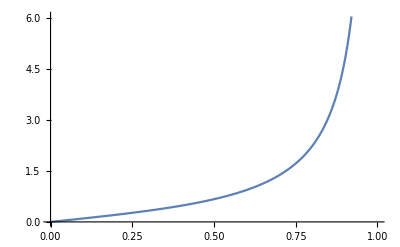

```mathematica
Plot[y/(1-y^2),{y,0,1}]
```

```mathematica
((1+√(1+4 ν^2))^(k-1)-(1-√(1+4 ν^2))^(k-1))/(2^(k-1)√(1+4 ν^2)) ν^(n-k+1)+(-1)^(k-1)ν^(k-1)((1+√(1+4 ν^2))^(n-k+1)-(1-√(1+4 ν^2))^(n-k+1))/(2^(n-k+1)√(1+4 ν^2))/.ν->y/(1-y^2)
```

```mathematica
Simplify[(2^(1-k) (y/(1-y^2))^(1-k+n) (-(1-√(1+(4 y^2)/((1-y^2)^2)))^(-1+k)+(1+√(1+(4 y^2)/((1-y^2)^2)))^(-1+k)))/(√(1+(4 y^2)/((1-y^2)^2)))+((-1)^(-1+k) 2^(-1+k-n) (y/(1-y^2))^(-1+k) (-(1-√(1+(4 y^2)/((1-y^2)^2)))^(1-k+n)+(1+√(1+(4 y^2)/((1-y^2)^2)))^(1-k+n)))/(√(1+(4 y^2)/((1-y^2)^2))),0<y<1]
```

(y^-k (1-y^2) (-(-1+(-y)^n) (1/y-y)^-n y^2+(-y^2)^k (1-y^2)^-n (-1+y^n)))/(y+y^3)

To study the sign, it is enough to study the right factor of the numerator:

```mathematica
(-(-1+(-y)^n) (1/y-y)^-n y^2+(-y^2)^k (1-y^2)^-n (-1+y^n))
```

```mathematica
(1-y^2)^-n (y^(2+n)-(-y)^n y^(2+n)-(-y^2)^k+y^n (-y^2)^k)
```

Or this quantity: we take into account that n should be odd; 1≤k≤2m+1

```mathematica
y^(2+n)-(-y)^n y^(2+n)-(-y^2)^k+y^n (-y^2)^k/.n->2m+1
```

y^(3+2 m)-(-y)^(1+2 m) y^(3+2 m)-(-y^2)^k+y^(1+2 m) (-y^2)^k

```mathematica
y^(3+2 m)-(-1)^(1+2 m)(y)^(1+2 m) y^(3+2 m)-(-y^2)^k+y^(1+2 m) (-y^2)^k
```

```mathematica
y^(3+2 m)+(-1)^(2+2 m) y^(4+4 m)-(-1)^k(y)^(2k)+(-1)^k y^(1+2 m) (y)^(2k)
```

```mathematica
(-1)^(1+k) y^(2 k)+y^(3+2 m)+(-1)^k y^(1+2 k+2 m)+(-1)^(2+2 m) y^(4+4 m)
```

```mathematica
(-1)^(1+k) y^(2 k)+y^(3+2 m)+(-1)^k y^(1+2 k+2 m)+ y^(4+4 m)
```

(-1)^(1+k) y^(2 k)+y^(3+2 m)+(-1)^k y^(1+2 k+2 m)+y^(4+4 m)

### So the signs of the entries are governed by the following set of lacunary polynomials: inverse matrix size = n = 2m+1, entry position in the first row = k with 1≤k≤2m+1; and we have seen that it is enough to consider the case k=2L. Here 1≤L≤m.

```mathematica
(-1)^(1+k) y^(2 k)+y^(3+2 m)+(-1)^k y^(1+2 k+2 m)+y^(4+4 m)/.k->2L
```

(-1)^(1+2 L) y^(4 L)+y^(3+2 m)+(-1)^(2 L) y^(1+4 L+2 m)+y^(4+4 m)

```mathematica
- y^(4 L)+y^(3+2 m)+ y^(1+4 L+2 m)+y^(4+4 m)
```

-y^(4 L)+y^(3+2 m)+y^(1+4 L+2 m)+y^(4+4 m)

### We should focus on this: 1≤L≤m.

```mathematica
-y^(4 L)+y^(3+2 m)+y^(1+4 L+2 m)+y^(4+4 m)
```

-y^(4 L)+y^(3+2 m)+y^(1+4 L+2 m)+y^(4+4 m)

### Let us fix y∈(0,1) and define poly_(m,L)(y):=-y^(4 L)+y^(3+2 m)+y^(1+4 L+2 m)+y^(4+4 m). Clearly, poly_(m,L)(0)=0, poly_(m,L)(1)=2, and poly_(m,L)(y)<poly_(m,L+1)(y):

```mathematica
(-y^(4 L)+y^(3+2 m)+y^(1+4 L+2 m)+y^(4+4 m)/.L->L+1)-(-y^(4 L)+y^(3+2 m)+y^(1+4 L+2 m)+y^(4+4 m))==y^(4 L) (1-y^4) (1-y^(1+2 m))//Simplify
```

True

### We also know that, for a fixed m, poly_(m,1) has a unique positive root y^*∈(0,1): poly_(m,1)<0 on (0,y^*), and poly_(m,1)>0 on (y^*,1). So the polynomials poly_(m,L) for any 1<L CANNOT have larger roots than y^*.

# This means that the overall sign behavior of the inverse matrix is governed by the entry inverse_(1,2) as conjectured.

```mathematica
Manipulate[Plot[-y^(4 L)+y^(3+2 m)+y^(1+4 L+2 m)+y^(4+4 m),{y,0,1},PlotRange->{-1,4}],{L,1,m,1},{m,2,10,1}]
```

# Connection with the trig formula. Further recursions. The explicit formula for the first row of the inverse matrix: for matrix size n (n≥2), the element of the inverse at position k (1≤k≤n) multiplied by the det of the original matrix is

### ((1+√(1+4 ν^2))^(k-1)-(1-√(1+4 ν^2))^(k-1))/(2^(k-1)√(1+4 ν^2)) ν^(n-k+1)+(-1)^(k-1)ν^(k-1)((1+√(1+4 ν^2))^(n-k+1)-(1-√(1+4 ν^2))^(n-k+1))/(2^(n-k+1)√(1+4 ν^2)) or, after an index shift in the trig formula, det[original matrix_(n x n)] 1/n Sum[(1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n])^-1 Exp[-(2π I)/nj (k-1)],{j,0,n-1}] in other words, Product[1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n],{j,0,n-1}]/n Sum[ⅇ^(-(2 ⅈ j (-1+k) π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}].

### We know the brown formula from the general theory. We’ve proved the green formula above. Corollary. As a by-product, we have that the second brown formula is equal to the green formula. Remark. They both satisfy the following linear recursion for n≥3 and 1≤k≤n-2 (n,k integers): firstrowOfTheInverse[k+2]==1/ν firstrowOfTheInverse[k+1]+firstrowOfTheInverse[k] with initialization firstrowOfTheInverse[1]==(2^-n (-(1-√(1+4 ν^2))^n+(1+√(1+4 ν^2))^n))/(√(1+4 ν^2)),firstrowOfTheInverse[2]==ν^(-1+n)-(2^(1-n) ν (-(1-√(1+4 ν^2))^(-1+n)+(1+√(1+4 ν^2))^(-1+n)))/(√(1+4 ν^2)).

```mathematica
(((1+√(1+4 ν^2))^(k-1)-(1-√(1+4 ν^2))^(k-1))/(2^(k-1)√(1+4 ν^2)) ν^(n-k+1)+(-1)^(k-1)ν^(k-1)((1+√(1+4 ν^2))^(n-k+1)-(1-√(1+4 ν^2))^(n-k+1))/(2^(n-k+1)√(1+4 ν^2))/.k->k+2)==1/ν(((1+√(1+4 ν^2))^(k-1)-(1-√(1+4 ν^2))^(k-1))/(2^(k-1)√(1+4 ν^2)) ν^(n-k+1)+(-1)^(k-1)ν^(k-1)((1+√(1+4 ν^2))^(n-k+1)-(1-√(1+4 ν^2))^(n-k+1))/(2^(n-k+1)√(1+4 ν^2))/.k->k+1)+(((1+√(1+4 ν^2))^(k-1)-(1-√(1+4 ν^2))^(k-1))/(2^(k-1)√(1+4 ν^2)) ν^(n-k+1)+(-1)^(k-1)ν^(k-1)((1+√(1+4 ν^2))^(n-k+1)-(1-√(1+4 ν^2))^(n-k+1))/(2^(n-k+1)√(1+4 ν^2)))//Simplify
```

True

### Direct check:

```mathematica
RSolve[firstrowOfTheInverse[k+2]==1/ν firstrowOfTheInverse[k+1]+firstrowOfTheInverse[k],firstrowOfTheInverse[k],k]
```

{{firstrowOfTheInverse[k]→2^-k (-√(4+1/ν^2)+1/ν)^k C[1]+2^-k (√(4+1/ν^2)+1/ν)^k C[2]}}

```mathematica
RSolve[{firstrowOfTheInverse[k+2]==1/ν firstrowOfTheInverse[k+1]+firstrowOfTheInverse[k],firstrowOfTheInverse[1]==(2^-n (-(1-√(1+4 ν^2))^n+(1+√(1+4 ν^2))^n))/(√(1+4 ν^2)),firstrowOfTheInverse[2]==ν^(-1+n)-(2^(1-n) ν (-(1-√(1+4 ν^2))^(-1+n)+(1+√(1+4 ν^2))^(-1+n)))/(√(1+4 ν^2))},firstrowOfTheInverse[k],k]
```

```mathematica
{{firstrowOfTheInverse[k]->1/(√(4+1/ν^2) ν^2 √(1+4 ν^2))2^(-2-k-n) (2^(1+n) ((-√(4+1/ν^2)+1/ν)^k-(√(4+1/ν^2)+1/ν)^k) ν^n √(1+4 ν^2)+2^(1+n) ((-√(4+1/ν^2)+1/ν)^k+(√(4+1/ν^2)+1/ν)^k) √(4+1/ν^2) ν^(1+n) √(1+4 ν^2)+4 ((-√(4+1/ν^2)+1/ν)^k-(√(4+1/ν^2)+1/ν)^k) ν^2 ((1-√(1+4 ν^2))^n-(1+√(1+4 ν^2))^n)-((-√(4+1/ν^2)+1/ν)^k-(√(4+1/ν^2)+1/ν)^k) (-(1-√(1+4 ν^2))^n+√(1+4 ν^2) (1-√(1+4 ν^2))^n+(1+√(1+4 ν^2))^n+√(1+4 ν^2) (1+√(1+4 ν^2))^n)-((-√(4+1/ν^2)+1/ν)^k+(√(4+1/ν^2)+1/ν)^k) √(4+1/ν^2) ν (-(1-√(1+4 ν^2))^n+√(1+4 ν^2) (1-√(1+4 ν^2))^n+(1+√(1+4 ν^2))^n+√(1+4 ν^2) (1+√(1+4 ν^2))^n))}}
```

```mathematica
FullSimplify[1/(√(4+1/ν^2) ν^2 √(1+4 ν^2))2^(-2-k-n) (2^(1+n) ((-√(4+1/ν^2)+1/ν)^k-(√(4+1/ν^2)+1/ν)^k) ν^n √(1+4 ν^2)+2^(1+n) ((-√(4+1/ν^2)+1/ν)^k+(√(4+1/ν^2)+1/ν)^k) √(4+1/ν^2) ν^(1+n) √(1+4 ν^2)+4 ((-√(4+1/ν^2)+1/ν)^k-(√(4+1/ν^2)+1/ν)^k) ν^2 ((1-√(1+4 ν^2))^n-(1+√(1+4 ν^2))^n)-((-√(4+1/ν^2)+1/ν)^k-(√(4+1/ν^2)+1/ν)^k) (-(1-√(1+4 ν^2))^n+√(1+4 ν^2) (1-√(1+4 ν^2))^n+(1+√(1+4 ν^2))^n+√(1+4 ν^2) (1+√(1+4 ν^2))^n)-((-√(4+1/ν^2)+1/ν)^k+(√(4+1/ν^2)+1/ν)^k) √(4+1/ν^2) ν (-(1-√(1+4 ν^2))^n+√(1+4 ν^2) (1-√(1+4 ν^2))^n+(1+√(1+4 ν^2))^n+√(1+4 ν^2) (1+√(1+4 ν^2))^n)),{ν>0,n∈Integers,k∈Integers}]
```

1/(√(1+4 ν^2))2^(-1-k-n) ν^(-1-3 k) (2^n ν^n (-ν^2 (-1+√(1+4 ν^2)))^k (1+√(1+4 ν^2))+2^n ν^(2 k+n) (-1+√(1+4 ν^2)) (1+√(1+4 ν^2))^k-ν^(2 k) (-(1-√(1+4 ν^2))^n (1+√(1+4 ν^2))^k+√(1+4 ν^2) (1-√(1+4 ν^2))^n (1+√(1+4 ν^2))^k+(1-√(1+4 ν^2))^k (1+√(1+4 ν^2))^n+√(1+4 ν^2) (1-√(1+4 ν^2))^k (1+√(1+4 ν^2))^n))

```mathematica
Simplify[1/(√(1+4 ν^2))2^(-1-k-n) ν^(-1-3 k) (2^n ν^n (-ν^2 (-1+√(1+4 ν^2)))^k (1+√(1+4 ν^2))+2^n ν^(2 k+n) (-1+√(1+4 ν^2)) (1+√(1+4 ν^2))^k-ν^(2 k) (-(1-√(1+4 ν^2))^n (1+√(1+4 ν^2))^k+√(1+4 ν^2) (1-√(1+4 ν^2))^n (1+√(1+4 ν^2))^k+(1-√(1+4 ν^2))^k (1+√(1+4 ν^2))^n+√(1+4 ν^2) (1-√(1+4 ν^2))^k (1+√(1+4 ν^2))^n))==((1+√(1+4 ν^2))^(k-1)-(1-√(1+4 ν^2))^(k-1))/(2^(k-1)√(1+4 ν^2)) ν^(n-k+1)+(-1)^(k-1)ν^(k-1)((1+√(1+4 ν^2))^(n-k+1)-(1-√(1+4 ν^2))^(n-k+1))/(2^(n-k+1)√(1+4 ν^2)),{ν>0,n∈Integers,k∈Integers}]
```

True

### What does it mean for the trig representation to satisfy the linear recursion firstrowOfTheInverse[k+2]==1/ν firstrowOfTheInverse[k+1]+firstrowOfTheInverse[k]? Of course, here 1≤ k≤n-2, and n≥3.

```mathematica
With[{n=2},Sum[ⅇ^(-(2 ⅈ j (+1+k) π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]-1/ν Sum[ⅇ^(-(2 ⅈ j k  π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]-Sum[ⅇ^(-(2 ⅈ j (-1+k) π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]]
```

```mathematica
-ⅇ^(-ⅈ (-1+k) π)+ⅇ^(-ⅈ (1+k) π)-(1+ⅇ^(-ⅈ k π))/ν//Simplify
```

```mathematica
-(1+ⅇ^(-ⅈ k π))/ν/.k->{0,1}
```

{-2/ν,0}

```mathematica
With[{n=3,k=1},Sum[ⅇ^(-(2 ⅈ j (+1+k) π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]-1/ν Sum[ⅇ^(-(2 ⅈ j k  π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]-Sum[ⅇ^(-(2 ⅈ j (-1+k) π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]]
```

```mathematica
-1/(1-ⅈ √3 ν)+ⅇ^(-(2 ⅈ π)/3)/(1-ⅈ √3 ν)-1/(1+ⅈ √3 ν)+ⅇ^((2 ⅈ π)/3)/(1+ⅈ √3 ν)-(1+ⅇ^((2 ⅈ π)/3)/(1-ⅈ √3 ν)+ⅇ^(-(2 ⅈ π)/3)/(1+ⅈ √3 ν))/ν//Simplify
```

0

```mathematica
With[{n=4,k=1},Sum[ⅇ^(-(2 ⅈ j (+1+k) π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]-1/ν Sum[ⅇ^(-(2 ⅈ j k  π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]-Sum[ⅇ^(-(2 ⅈ j (-1+k) π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]]//Simplify
```

0

```mathematica
With[{n=4,k=2},Sum[ⅇ^(-(2 ⅈ j (+1+k) π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]-1/ν Sum[ⅇ^(-(2 ⅈ j k  π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]-Sum[ⅇ^(-(2 ⅈ j (-1+k) π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]]//Simplify
```

0

```mathematica
With[{n=7},Sum[ⅇ^(-(2 ⅈ j (+1+k) π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]-1/ν Sum[ⅇ^(-(2 ⅈ j k  π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]-Sum[ⅇ^(-(2 ⅈ j (-1+k) π)/n)/(1-2 ⅈ ⅇ^(ⅈ j π) ν Sin[(j (-2+n) π)/n]),{j,0,n-1}]]
```

-ⅇ^(-10/7 ⅈ (-1+k) π)/(1-2 ⅈ ν Cos[π/14])+ⅇ^(-10/7 ⅈ (1+k) π)/(1-2 ⅈ ν Cos[π/14])-ⅇ^(-4/7 ⅈ (-1+k) π)/(1+2 ⅈ ν Cos[π/14])+ⅇ^(-4/7 ⅈ (1+k) π)/(1+2 ⅈ ν Cos[π/14])-ⅇ^(-12/7 ⅈ (-1+k) π)/(1-2 ⅈ ν Cos[(3 π)/14])+ⅇ^(-12/7 ⅈ (1+k) π)/(1-2 ⅈ ν Cos[(3 π)/14])-ⅇ^(-2/7 ⅈ (-1+k) π)/(1+2 ⅈ ν Cos[(3 π)/14])+ⅇ^(-2/7 ⅈ (1+k) π)/(1+2 ⅈ ν Cos[(3 π)/14])-ⅇ^(-8/7 ⅈ (-1+k) π)/(1-2 ⅈ ν Sin[π/7])+ⅇ^(-8/7 ⅈ (1+k) π)/(1-2 ⅈ ν Sin[π/7])-ⅇ^(-6/7 ⅈ (-1+k) π)/(1+2 ⅈ ν Sin[π/7])+ⅇ^(-6/7 ⅈ (1+k) π)/(1+2 ⅈ ν Sin[π/7])-(1+ⅇ^(-10/7 ⅈ k π)/(1-2 ⅈ ν Cos[π/14])+ⅇ^(-4/7 ⅈ k π)/(1+2 ⅈ ν Cos[π/14])+ⅇ^(-12/7 ⅈ k π)/(1-2 ⅈ ν Cos[(3 π)/14])+ⅇ^(-2/7 ⅈ k π)/(1+2 ⅈ ν Cos[(3 π)/14])+ⅇ^(-8/7 ⅈ k π)/(1-2 ⅈ ν Sin[π/7])+ⅇ^(-6/7 ⅈ k π)/(1+2 ⅈ ν Sin[π/7]))/ν

```mathematica
FullSimplify[-ⅇ^(-10/7 ⅈ (-1+k) π)/(1-2 ⅈ ν Cos[π/14])+ⅇ^(-10/7 ⅈ (1+k) π)/(1-2 ⅈ ν Cos[π/14])-ⅇ^(-4/7 ⅈ (-1+k) π)/(1+2 ⅈ ν Cos[π/14])+ⅇ^(-4/7 ⅈ (1+k) π)/(1+2 ⅈ ν Cos[π/14])-ⅇ^(-12/7 ⅈ (-1+k) π)/(1-2 ⅈ ν Cos[(3 π)/14])+ⅇ^(-12/7 ⅈ (1+k) π)/(1-2 ⅈ ν Cos[(3 π)/14])-ⅇ^(-2/7 ⅈ (-1+k) π)/(1+2 ⅈ ν Cos[(3 π)/14])+ⅇ^(-2/7 ⅈ (1+k) π)/(1+2 ⅈ ν Cos[(3 π)/14])-ⅇ^(-8/7 ⅈ (-1+k) π)/(1-2 ⅈ ν Sin[π/7])+ⅇ^(-8/7 ⅈ (1+k) π)/(1-2 ⅈ ν Sin[π/7])-ⅇ^(-6/7 ⅈ (-1+k) π)/(1+2 ⅈ ν Sin[π/7])+ⅇ^(-6/7 ⅈ (1+k) π)/(1+2 ⅈ ν Sin[π/7])-(1+ⅇ^(-10/7 ⅈ k π)/(1-2 ⅈ ν Cos[π/14])+ⅇ^(-4/7 ⅈ k π)/(1+2 ⅈ ν Cos[π/14])+ⅇ^(-12/7 ⅈ k π)/(1-2 ⅈ ν Cos[(3 π)/14])+ⅇ^(-2/7 ⅈ k π)/(1+2 ⅈ ν Cos[(3 π)/14])+ⅇ^(-8/7 ⅈ k π)/(1-2 ⅈ ν Sin[π/7])+ⅇ^(-6/7 ⅈ k π)/(1+2 ⅈ ν Sin[π/7]))/ν,{k∈Integers,1≤k≤5,ν>0}]
```

-(ⅇ^(-6/7 ⅈ k π) (1+2 Cos[(2 k π)/7]+2 Cos[(4 k π)/7]+2 Cos[(6 k π)/7]))/ν

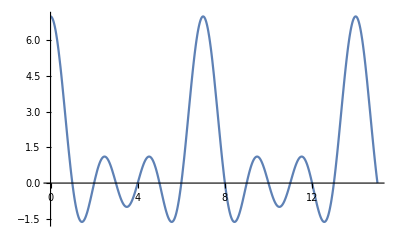

```mathematica
Plot[1+2 Cos[(2 k π)/7]+2 Cos[(4 k π)/7]+2 Cos[(6 k π)/7],{k,0,15}]
```

```mathematica
Table[1+2 Cos[(2 k π)/7]+2 Cos[(4 k π)/7]+2 Cos[(6 k π)/7],{k,0,6}]
```

```mathematica
{7,1-2 Cos[π/7]-2 Sin[π/14]+2 Sin[(3 π)/14],1-2 Cos[π/7]-2 Sin[π/14]+2 Sin[(3 π)/14],1-2 Cos[π/7]-2 Sin[π/14]+2 Sin[(3 π)/14],1-2 Cos[π/7]-2 Sin[π/14]+2 Sin[(3 π)/14],1-2 Cos[π/7]-2 Sin[π/14]+2 Sin[(3 π)/14],1-2 Cos[π/7]-2 Sin[π/14]+2 Sin[(3 π)/14]}//N//Chop
```

{7.,0,0,0,0,0,0}

### Nice trig identities are obtained.

# Earlier computations:

Transformations for the element inverse_(1,3):

```mathematica
Det@({{ν, 0, 0, 0, 0, 0, -ν}, {1, ν, 0, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}})==ν^2 Det@({{1, ν, 0, 0, 0}, {-ν, 1, ν, 0, 0}, {0, -ν, 1, ν, 0}, {0, 0, -ν, 1, ν}, {0, 0, 0, -ν, 1}})-ν Det@({{-ν, 1, ν, 0, 0}, {0, -ν, 1, ν, 0}, {0, 0, -ν, 1, ν}, {0, 0, 0, -ν, 1}, {0, 0, 0, 0, -ν}})//Expand
```

True

Transformations for the element inverse_(1,4):

```mathematica
-Det@({{ν, 0, 0, 0, 0, 0, -ν}, {1, ν, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}})==-ν^3 Det@({{1, ν, 0, 0}, {-ν, 1, ν, 0}, {0, -ν, 1, ν}, {0, 0, -ν, 1}})+ν Det@({{1, ν, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0}, {0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, -ν, 1}, {0, 0, 0, 0, 0, -ν}})==-ν^3 Det@({{1, ν, 0, 0}, {-ν, 1, ν, 0}, {0, -ν, 1, ν}, {0, 0, -ν, 1}})+ν (Det@({{1, ν, 0, 0, 0}, {0, -ν, 1, ν, 0}, {0, 0, -ν, 1, ν}, {0, 0, 0, -ν, 1}, {0, 0, 0, 0, -ν}})+ν Det@({{ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0}, {0, 0, -ν, 1, ν}, {0, 0, 0, -ν, 1}, {0, 0, 0, 0, -ν}}))==-ν^3 Det@({{1, ν, 0, 0}, {-ν, 1, ν, 0}, {0, -ν, 1, ν}, {0, 0, -ν, 1}})+ν ((-ν)^4+ν^6)//Expand
```

True

Transformations for the element inverse_(1,5):

```mathematica
Det@({{ν, 0, 0, 0, 0, 0, -ν}, {1, ν, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, 0, -ν, 1, ν, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}})==ν Det@({{ν, 0, 0, 0, 0, 0}, {1, ν, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0}, {0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, -ν, 1}})-ν Det@({{1, ν, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0}, {0, -ν, 1, ν, 0, 0}, {0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, -ν, 1}, {0, 0, 0, 0, 0, -ν}})==ν^4 Det@({{1, ν, 0}, {-ν, 1, ν}, {0, -ν, 1}})-ν (Det@({{1, ν, 0, 0, 0}, {-ν, 1, ν, 0, 0}, {0, 0, -ν, 1, ν}, {0, 0, 0, -ν, 1}, {0, 0, 0, 0, -ν}})-ν Det@({{-ν, ν, 0, 0, 0}, {0, 1, ν, 0, 0}, {0, 0, -ν, 1, ν}, {0, 0, 0, -ν, 1}, {0, 0, 0, 0, -ν}}))==ν^4 Det@({{1, ν, 0}, {-ν, 1, ν}, {0, -ν, 1}})-ν (Det@({{1, ν, 0, 0}, {0, -ν, 1, ν}, {0, 0, -ν, 1}, {0, 0, 0, -ν}})-ν Det@({{-ν, ν, 0, 0}, {0, -ν, 1, ν}, {0, 0, -ν, 1}, {0, 0, 0, -ν}})-ν^5)==ν^4 Det@({{1, ν, 0}, {-ν, 1, ν}, {0, -ν, 1}})-ν (-ν^3-ν^5-ν^5)//Expand
```

True

Transformations for the element inverse_(1,6):

```mathematica
Det@({{ν, 0, 0, 0, 0, 0, -ν}, {1, ν, 0, 0, 0, 0, 0}, {-ν, 1, ν, 0, 0, 0, 0}, {0, -ν, 1, ν, 0, 0, 0}, {0, 0, -ν, 1, ν, 0, 0}, {0, 0, 0, 0, -ν, 1, ν}, {0, 0, 0, 0, 0, -ν, 1}})==ν^5 Det@({{1, ν}, {-ν, 1}})-ν (Det@({{1, ν, 0, 0, 0}, {-ν, 1, ν, 0, 0}, {0, -ν, 1, ν, 0}, {0, 0, 0, -ν, 1}, {0, 0, 0, 0, -ν}})+ν^2 Det@({{1, ν, 0, 0}, {-ν, 1, ν, 0}, {0, 0, -ν, 1}, {0, 0, 0, -ν}}) )==ν^5 Det@({{1, ν}, {-ν, 1}})-ν (Det@({{1, ν, 0, 0}, {-ν, 1, ν, 0}, {0, 0, -ν, 1}, {0, 0, 0, -ν}})-ν Det@({{-ν, ν, 0, 0}, {0, 1, ν, 0}, {0, 0, -ν, 1}, {0, 0, 0, -ν}})+ν^2 (Det@({{1, ν, 0}, {0, -ν, 1}, {0, 0, -ν}}) -ν Det@({{-ν, ν, 0}, {0, -ν, 1}, {0, 0, -ν}})  ) )==ν^5 Det@({{1, ν}, {-ν, 1}})-ν (Det@({{1, ν, 0, 0}, {-ν, 1, ν, 0}, {0, 0, -ν, 1}, {0, 0, 0, -ν}})+ν^4 +ν^2 (ν^2+ν^4 ) )==ν^5 Det@({{1, ν}, {-ν, 1}})-ν ((ν^2+ν^4)+ν^4 +ν^2 (ν^2+ν^4 ) )//Expand
```

True

```mathematica
ν ((ν^2+ν^4)+ν^4 +ν^2 (ν^2+ν^4 ) )//Expand
```

ν^3+3 ν^5+ν^7

### The det seems to be always a positive polynomial:

```mathematica
Table[det[m],{m,2,20}]
```

{1+ν^2,1+3 ν^2,1+4 ν^2,1+5 ν^2+5 ν^4,1+6 ν^2+9 ν^4,1+7 ν^2+14 ν^4+7 ν^6,1+8 ν^2+20 ν^4+16 ν^6,1+9 ν^2+27 ν^4+30 ν^6+9 ν^8,1+10 ν^2+35 ν^4+50 ν^6+25 ν^8,1+11 ν^2+44 ν^4+77 ν^6+55 ν^8+11 ν^10,1+12 ν^2+54 ν^4+112 ν^6+105 ν^8+36 ν^10,1+13 ν^2+65 ν^4+156 ν^6+182 ν^8+91 ν^10+13 ν^12,1+14 ν^2+77 ν^4+210 ν^6+294 ν^8+196 ν^10+49 ν^12,1+15 ν^2+90 ν^4+275 ν^6+450 ν^8+378 ν^10+140 ν^12+15 ν^14,1+16 ν^2+104 ν^4+352 ν^6+660 ν^8+672 ν^10+336 ν^12+64 ν^14,1+17 ν^2+119 ν^4+442 ν^6+935 ν^8+1122 ν^10+714 ν^12+204 ν^14+17 ν^16,1+18 ν^2+135 ν^4+546 ν^6+1287 ν^8+1782 ν^10+1386 ν^12+540 ν^14+81 ν^16,1+19 ν^2+152 ν^4+665 ν^6+1729 ν^8+2717 ν^10+2508 ν^12+1254 ν^14+285 ν^16+19 ν^18,1+20 ν^2+170 ν^4+800 ν^6+2275 ν^8+4004 ν^10+4290 ν^12+2640 ν^14+825 ν^16+100 ν^18}

### For EVEN m: the second element in the first row seems always to be a negative polynomial: cf. the last element in the same row. Proved above.

### For ODD m: the lower positive bound for ν seems to be determined by the (1,2) polynomial.

### From now on we consider only the case of odd m. We will have m=2n+1, and use only n. The numerators of the (1,2) elements satisfy the following recursion:

```mathematica
FindLinearRecurrence[{(-1+ν) ν,ν (-1-2 ν^2+ν^3),ν (-1-4 ν^2-3 ν^4+ν^5),ν (-1-6 ν^2-10 ν^4-4 ν^6+ν^7),ν (-1-8 ν^2-21 ν^4-20 ν^6-5 ν^8+ν^9),ν (-1-10 ν^2-36 ν^4-56 ν^6-35 ν^8-6 ν^10+ν^11),ν (-1-12 ν^2-55 ν^4-120 ν^6-126 ν^8-56 ν^10-7 ν^12+ν^13),ν (-1-14 ν^2-78 ν^4-220 ν^6-330 ν^8-252 ν^10-84 ν^12-8 ν^14+ν^15),ν (-1-16 ν^2-105 ν^4-364 ν^6-715 ν^8-792 ν^10-462 ν^12-120 ν^14-9 ν^16+ν^17)}]
```

{1+3 ν^2,-ν^2-3 ν^4,ν^6}

### That is:

```mathematica
RecurrenceTable[{second[n+3]==(1+3 ν^2)second[n+2]-(ν^2+3 ν^4) second[n+1]+ν^6 second[n],second[1]==-1+ν,second[2]==-1-2 ν^2+ν^3,second[3]==-1-4 ν^2-3 ν^4+ν^5},second,{n,1,9}]//Expand
```

{-1+ν,-1-2 ν^2+ν^3,-1-4 ν^2-3 ν^4+ν^5,-1-6 ν^2-10 ν^4-4 ν^6+ν^7,-1-8 ν^2-21 ν^4-20 ν^6-5 ν^8+ν^9,-1-10 ν^2-36 ν^4-56 ν^6-35 ν^8-6 ν^10+ν^11,-1-12 ν^2-55 ν^4-120 ν^6-126 ν^8-56 ν^10-7 ν^12+ν^13,-1-14 ν^2-78 ν^4-220 ν^6-330 ν^8-252 ν^10-84 ν^12-8 ν^14+ν^15,-1-16 ν^2-105 ν^4-364 ν^6-715 ν^8-792 ν^10-462 ν^12-120 ν^14-9 ν^16+ν^17}

### With explicit solution:

```mathematica
RSolve[{second[n+3]==(1+3 ν^2)second[n+2]-(ν^2+3 ν^4) second[n+1]+ν^6 second[n],second[1]==-1+ν,second[2]==-1-2 ν^2+ν^3,second[3]==-1-4 ν^2-3 ν^4+ν^5},second[n],n]
```

{{second[n]→(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))}}

### Thus we have an explicit formula for the polynomials in the numerators of the rational functions at position (1,2), which (assuming that the element (1,2) has the largest positive root) determines the critical ν>0 value (guaranteeing positivity of all entries of the matrix, under this assumption).

### These are indeed polynomials:

```mathematica
Table[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2)),{n,1,6}]//Simplify
```

{-1+ν,-1-2 ν^2+ν^3,-1-4 ν^2-3 ν^4+ν^5,-1-6 ν^2-10 ν^4-4 ν^6+ν^7,-1-8 ν^2-21 ν^4-20 ν^6-5 ν^8+ν^9,-1-10 ν^2-36 ν^4-56 ν^6-35 ν^8-6 ν^10+ν^11}

### The first few critical ν>0 values numerically:

```mathematica
N[Table[Reduce[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))>0],{n,1,30}],20]
```

{ν>1.,ν>2.2055694304005903117,ν>3.3617657267144615732,ν>4.5069633965305057749,ν>5.6478748967865146115,ν>6.7866658033191965387,ν>7.9242514529216698125,ν>9.0610861788817023851,ν>10.197421287623980626,ν>11.333407136290336656,ν>12.469139220581783219,ν>13.604681115388041778,ν>14.740076788426239465,ν>15.875357620320218936,ν>17.010546609277172976,ν>18.145660995444771567,ν>19.280713957200392349,ν>20.41571574103175839,ν>21.550674434065819794,ν>22.685596504521694258,ν>23.820487187558640086,ν>24.955350765775926473,ν>26.090190776465082208,ν>27.225010167001471683,ν>28.359811412910516288,ν>29.494596608666797425,ν>30.629367538301192434,ν>31.764125730867927873,ν>32.898872504428665255,ν>34.033609001234758888}

```mathematica
N[Table[Reduce[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))>0],{n,30,60}],20]
```

{ν>34.033609001234758888,ν>35.168336216096426329,ν>36.303055019430056786,ν>37.437766176113149008,ν>38.572470361010452672,ν>39.707168171837390887,ν>40.841860139878747892,ν>41.976546738968555037,ν>43.111228393051609298,ν>44.245905482581299925,ν>45.38057834995746271,ν>46.515247304168215711,ν>47.649912624768489365,ν>48.784574565303264399,ν>49.919233356263885581,ν>51.053889207650104395,ν>52.188542311197864561,ν>53.32319284232262617,ν>54.457840961819722616,ν>55.592486817356468085,ν>56.727130544785177138,ν>57.861772269301682388,ν>58.996412106470152966,ν>60.131050163131875668,ν>61.26568653821304359,ν>62.400321323444408192,ν>63.534954604003813861,ν>64.669586459091087154,ν>65.804216962443446183,ν>66.93884618279848819,ν>68.073474184310872153}

# Normalized by n:

```mathematica
N[Table[Reduce[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))>0]/.(ν>a_->a/n),{n,2,40}],20]
```

{1.1027847152002951559,1.1205885755714871911,1.1267408491326264437,1.1295749793573029223,1.1311109672198660898,1.1320359218459528304,1.1326357723602127981,1.1330468097359978473,1.1333407136290336656,1.1335581109619802926,1.1337234262823368148,1.1338520606481722666,1.1339541157371584954,1.1340364406184781984,1.1341038122152982229,1.13415964454119955,1.1342064300573199106,1.1342460228455694629,1.1342798252260847129,1.1343089136932685755,1.1343341257170875669,1.1343561207158731395,1.1343754236250613201,1.1343924565164206515,1.134407561871799901,1.1344210199370812013,1.1344330618167117097,1.1344438794630574226,1.1344536333744919629,1.134462458583755688,1.1344704693571892746,1.1344777629125196669,1.1344844223826603727,1.1344905191953540253,1.1344961149966318859,1.1345012632153663523,1.1345060103434634026,1.1345103969892641006,1.1345144587489365677}

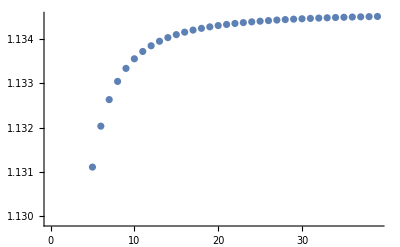

```mathematica
ListPlot[%]
```

```mathematica
N[Table[Reduce[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))>0]/.(ν>a_->a/n),{n,41,60}],20]
```

{1.1345182269309320905,1.1345217291611545087,1.1345249898907735907,1.1345280308241792177,1.134530871281113431,1.1345335285043014035,1.1345360179217580036,1.1345383533712442212,1.1345405472929891446,1.1345426108957035428,1.134544554300032988,1.134546386662887557,1.1345481162855070881,1.1345497507076489554,1.1345512967898983308,1.1345527607857823904,1.1345541484051067922,1.1345554648697145894,1.1345567149626862405,1.1345579030718478692}

```mathematica
N[Table[Reduce[(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))>0]/.(ν>a_->a/n),{n,61,80}],20]
```

{1.1345590332283280475,1.1345601091407967957,1.1345611342259306921,1.1345621116355721056,1.1345630442809862657,1.1345639348545652579,1.1345647858492814901,1.1345655995761534333,1.1345663781799524117,1.1345671236533500163,1.1345678378496805964,1.1345685224944716326,1.1345691791958760836,1.1345698094541246038,1.1345704146701014753,1.1345709961531358844,1.1345715551280895288,1.1345720927418122628,1.1345726100690293665,1.1345731081177169199}

### Conjecture: we have a limiting constant approx. 1.13457 (after the normalization).

# Simplifying observation:

### By using the new variable y==((1+2 ν^2-√(1+4 ν^2))/(1+2 ν^2+√(1+4 ν^2)))^(1/4)=(-1+√(1+4 ν^2))/(2 ν)∈(0,1), we transform the equation (2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))=0 to the lacunary polynomial y^(4 n)+y^(-1+2 n)+y^(1+2 n)==1.

### Remark: the inverse transformation (from y to ν) is ν→y/(1-y^2). This is a bijection between the variables ν∈(0,+∞) and y∈(0,1).

### So we investigate the roots of the equation y^(4 n)+y^(2 n+1)+y^(2 n-1)==1,

### or, in other words, those of the equation (1+y^(2 n-1)) (1+y^(1+2 n))==2.

### We know that 0<y<1. Hence we are to find positive roots. From e.g. the 1st form it is clear (due to strict monotonicity) that we have a unique positive y-root. Due to ν=y/(1-y^2), this means that we have a unique ν-root, which is the above-mentioned critical ν value.

### Heuristics: when y is close to 1, the two factors in (1+y^(2 n-1)) (1+y^(1+2 n))==2 are approx. equal. So, approximately,

```mathematica
y==(√2-1)^(1/(2n))
```

```mathematica
Series[(√2-1)^(1/(2n)),{n,∞,3}]//Normal
```

```mathematica
1+Log[-1+√2]/(2 n)+Log[-1+√2]^2/(8 n^2)+Log[-1+√2]^3/(48 n^3)//N
```

1.-0.0142639/n^3+0.0971024/n^2-0.440687/n

```mathematica
ν==y/(1-y^2)/.y->1+Log[-1+√2]/(2 n)//FullSimplify
```

```mathematica
ν==n (1/ArcSinh[1]+1/(-4 n+ArcSinh[1]))//N
```

ν==(1.13459+1/(0.881374-4. n)) n

### So most probably the first term of the asymptotic expansion of ν is n/ArcSinh[1]==n/Log[1+√2].

### This is the constant we had from the numerical experiments:

```mathematica
N[n/Log[1+√2],20]
```

1.1345926571065109841 n

### Let us consider the estimate y_n=1-Log[√(1+√2)]/n of the root of the lacunary polynomial.

```mathematica
(1+y^(2 n-1)) (1+y^(1+2 n))/.y->1-Log[√(1+√2)]/n
```

(1+(1-Log[1+√2]/(2 n))^(-1+2 n)) (1+(1-Log[1+√2]/(2 n))^(1+2 n))

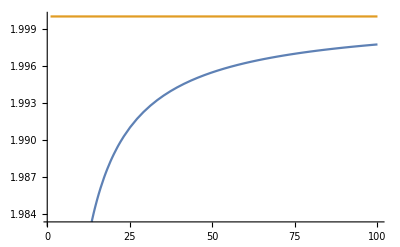

```mathematica
Plot[{(1+(1-Log[1+√2]/(2 n))^(-1+2 n)) (1+(1-Log[1+√2]/(2 n))^(1+2 n)),2},{n,1,100}]
```

```mathematica
Limit[(1+(1-Log[1+√2]/(2 n))^(-1+2 n)) (1+(1-Log[1+√2]/(2 n))^(1+2 n)),n->∞]
```

2

### So it seems that y_n=1-Log[√(1+√2)]/n is an (asymptotically optimal) lower bound. In terms of ν, this is

```mathematica
ν==y/(1-y^2)/.y->1-Log[√(1+√2)]/n//Simplify
```

```mathematica
ν==(4 n^2-2 n Log[1+√2])/(4 n Log[1+√2]-Log[1+√2]^2)//N
```

ν==(-1.76275 n+4. n^2)/(-0.776819+3.52549 n)

### We would like to exclude “bad” ν values. Therefore we now give a lower bound for ν.

```mathematica
Reduce[(4 n^2-2 n Log[1+√2])/(4 n Log[1+√2]-Log[1+√2]^2)>(4 n^2-2 n Log[1+√2])/(4 n Log[1+√2])]//N
```

n<0.220343||n>0.440687

```mathematica
(4 n^2-2 n Log[1+√2])/(4 n Log[1+√2])//Simplify
```

```mathematica
-1/2+n/Log[1+√2]//N
```

-0.5+1.13459 n

### So for this value, ν_*=n/Log[1+√2]-1/2≈1.13459 n -0.5, the polynomial is still negative (provided we prove the inequality (1+(1-Log[1+√2]/(2 n))^(-1+2 n)) (1+(1-Log[1+√2]/(2 n))^(1+2 n))<2).

### And it seems, that the polynomial is already positive for ν^*=n/Log[1+√2]≈1.13459 n .

### For y, this means

```mathematica
(-1+√(1+4 ν^2))/(2 ν)/.ν->n/Log[1+√2]//Simplify
```

```mathematica
(-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/(2 n)//Expand//N
```

```mathematica
(1+y^(2 n-1)) (1+y^(1+2 n))/.y->(-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/(2 n)
```

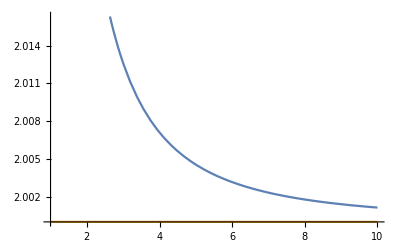

```mathematica
Plot[{(1+2^(1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(-1+2 n)) (1+2^(-1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(1+2 n)),2},{n,1,10}]
```

```mathematica
Limit[(1+2^(1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(-1+2 n)) (1+2^(-1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(1+2 n)),n->∞]
```

2

### Conclusion: if we prove (1+2^(1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(-1+2 n)) (1+2^(-1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(1+2 n))>2

### and (1+(1-Log[1+√2]/(2 n))^(-1+2 n)) (1+(1-Log[1+√2]/(2 n))^(1+2 n))<2, then we have SIMPLE, relatively SHARP, asymptotically OPTIMAL lower and upper bounds (ν_*=ν_(n, *) and ν^*=ν_n^* defined above) for the unique positive root of the element (1,2) (or, under the above assumption, for the critical ν-value itself). Still needs to be proved: – positivity of the determinants (appearing as denominators); – the various linear recursions (to be proved based on determinant expansions).

# Auxiliary material:

### The a_k quantities (i.e., elements of the first row of the inverse matrix, which is also circulant): these are rational functions

```mathematica
1/n Sum[(1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n])^-1 Exp[-(2π I)/n j k],{j,0,n-1}]
```

(∑_(j=0)^(-1+n) ⅇ^(-(2 ⅈ j k π)/n)/(1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n]))/n

### The k^th element of the first row of the circulant matrix multiplied by the determinant: these are polynomials

```mathematica
Product[1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n],{j,0,n-1}]/n Sum[(1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n])^-1 Exp[-(2π I)/n j k],{j,0,n-1}]
```

((∏_(j=0)^(-1+n) (1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n])) ∑_(j=0)^(-1+n) ⅇ^(-(2 ⅈ j k π)/n)/(1-2 ⅈ ν Cos[j π] Sin[(j (-2+n) π)/n]+2 ν Sin[j π] Sin[(j (-2+n) π)/n]))/n

### Establishing positivity of these quantities in terms of ν seems intractable.

# Proving the asymptotically optimal lower and upper estimates.

# Lower: (1+(1-Log[1+√2]/(2 n))^(-1+2 n)) (1+(1-Log[1+√2]/(2 n))^(1+2 n))<2

```mathematica
(1+(1-Log[1+√2]/(2 n))^(-1+2 n)) (1+(1-Log[1+√2]/(2 n))^(1+2 n))/.n->1//Simplify
```

(1+(1-1/2 Log[1+√2])^3) (2-1/2 Log[1+√2])

```mathematica
1-Log[1+√2]/(2 n)/.n->1.
```

0.559313

```mathematica
(1+(1-Log[1+√2]/(2 n))^(-1+2 n)) (1+(1-Log[1+√2]/(2 n))^(1+2 n))//Expand
```

1+(1-Log[1+√2]/(2 n))^(4 n)+(1-Log[1+√2]/(2 n))^(-1+2 n)+(1-Log[1+√2]/(2 n))^(1+2 n)

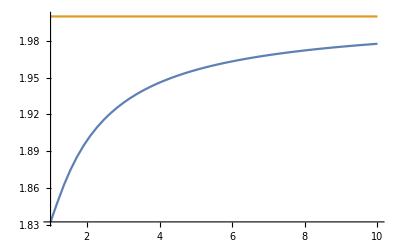

```mathematica
Plot[{1+(1-Log[1+√2]/(2 n))^(4 n)+(1-Log[1+√2]/(2 n))^(-1+2 n)+(1-Log[1+√2]/(2 n))^(1+2 n),2},{n,1,10}]
```

### Enough: (1-Log[1+√2]/(2 n))^(4 n)+(1-Log[1+√2]/(2 n))^(-1+2 n)+(1-Log[1+√2]/(2 n))^(1+2 n)<1 for n≥1.

```mathematica
Exp[4n Log[1-c/(2 n)]]+Exp[(2n-1) Log[1-c/(2 n)]]+Exp[(2n+1) Log[1-c/(2 n)]]<1
```

```mathematica
Log[1+√2]//N
```

0.881374

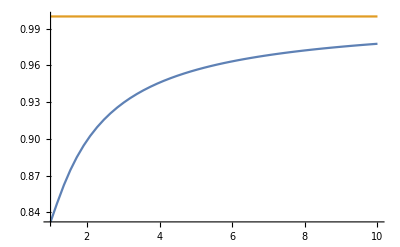

```mathematica
Plot[{Exp[4n Log[1-c/(2 n)]]+Exp[(2n-1) Log[1-c/(2 n)]]+Exp[(2n+1) Log[1-c/(2 n)]]/.c->Log[1+√2],1},{n,1,10}]
```

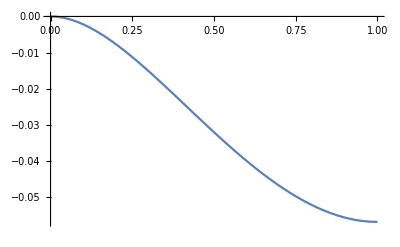

```mathematica
Plot[{Log[1+x]-(x-x^2/4)},{x,0,1}]
```

```mathematica
Reduce[Log[1+x]<(x-x^2/4)&&0<x<1]
```

0<x<1

```mathematica
Reduce[Log[1+x]<(x-x^2/4)]
```

-1<x<0||0<x<Root[{1+ⅇ^(-4 #1+#1^2) (-1-4 #1-6 #1^2-4 #1^3-#1^4)&,1.6237727561063439575}]

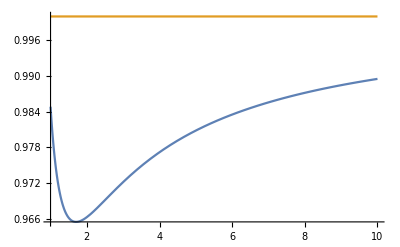

```mathematica
Plot[{Exp[4n (-c/(2 n)-1/4(c/(2 n))^2)]+Exp[(2n-1) (-c/(2 n)-1/4(c/(2 n))^2)]+Exp[(2n+1) (-c/(2 n)-1/4(c/(2 n))^2)]/.c->Log[1+√2],1},{n,1,10}]
```

```mathematica
Exp[-(c (c+8 n))/(4 n)]+Exp[-(c (-1+2 n) (c+8 n))/(16 n^2)]+Exp[-(c (1+2 n) (c+8 n))/(16 n^2)]<1
```

### Enough:

```mathematica
Exp[-2 c-c^2/(4 n)]+Exp[-c+c^2/(16 n^2)+c/(2 n)-c^2/(8 n)]+Exp[-c-c^2/(16 n^2)-c/(2 n)-c^2/(8 n)]<1
```

### Sufficient:

```mathematica
Exp[-2 c]+Exp[-c+c^2/(16 n^2)+c/(2 n)-c^2/(8 n)]+Exp[-c-c^2/(16 n^2)-c/(2 n)-c^2/(8 n)]<1
```

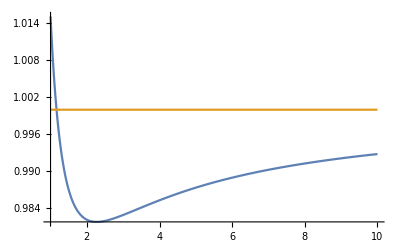

```mathematica
Plot[{Exp[-2 c-(0 c^2)/(4 n)]+Exp[-c+c^2/(16 n^2)+c/(2 n)-c^2/(8 n)]+Exp[-c-c^2/(16 n^2)-c/(2 n)-c^2/(8 n)],1}/.c->Log[1+√2]//Evaluate,{n,1,10}]
```

```mathematica
Exp[-2 c]+Exp[-c](Exp[c^2/(16 n^2)+c/(2 n)-c^2/(8 n)]+Exp[c^2/(16 n^2)-c/(2 n)-c^2/(8 n)])<1
```

```mathematica
+ (ⅇ^(c^2/(16 n^2)-c/(2 n)-c^2/(8 n))+ⅇ^(c^2/(16 n^2)+c/(2 n)-c^2/(8 n)))<(1-ⅇ^(-2 c))ⅇ^c
```

ⅇ^(c^2/(16 n^2)-c/(2 n)-c^2/(8 n))+ⅇ^(c^2/(16 n^2)+c/(2 n)-c^2/(8 n))<ⅇ^c (1-ⅇ^(-2 c))

```mathematica
ⅇ^c (1-ⅇ^(-2 c))/.c->Log[1+√2]//Simplify
```

2

### Enough:

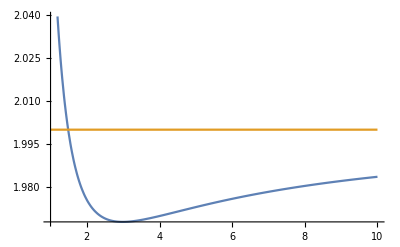

```mathematica
Plot[{ⅇ^(c^2/(16 n^2)-c/(2 n)-c^2/(8 n))+ⅇ^(c^2/(16 n^2)+c/(2 n)-c^2/(8 n)),2}/.c->Log[1+√2]//Evaluate,{n,1,10}]
```

```mathematica
ⅇ^(c^2/(16 n^2)-c/(2 n)-c^2/(8 n))+ⅇ^(c^2/(16 n^2)+c/(2 n)-c^2/(8 n))<2
```

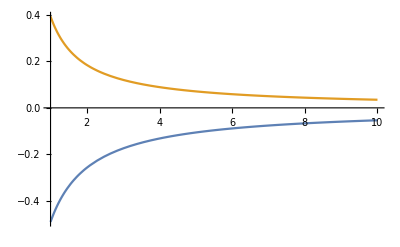

```mathematica
Plot[{c^2/(16 n^2)-c/(2 n)-c^2/(8 n),c^2/(16 n^2)+c/(2 n)-c^2/(8 n)}/.c->Log[1+√2]//Evaluate,{n,1,10}]
```

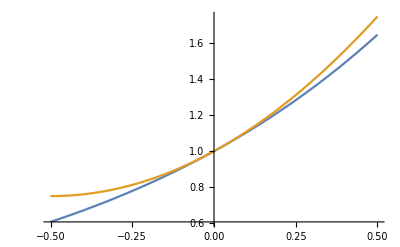

```mathematica
Plot[{Exp[x],1+x+x^2},{x,-.5,.5}]
```

```mathematica
Reduce[Exp[x]<1+x+x^2]
```

x<0||0<x<Root[{-1+ⅇ^#1-#1-#1^2&,1.7932821329007610076}]

```mathematica
ⅇ^(c^2/(16 n^2)-c/(2 n)-c^2/(8 n))+ⅇ^(c^2/(16 n^2)+c/(2 n)-c^2/(8 n))<2/.Exp[a_]->1+a+a^2
```

2+(c^2/(16 n^2)-c/(2 n)-c^2/(8 n))^2+(c^2/(16 n^2)+c/(2 n)-c^2/(8 n))^2+c^2/(8 n^2)-c^2/(4 n)<2

```mathematica
Reduce[2+(c^2/(16 n^2)-c/(2 n)-c^2/(8 n))^2+(c^2/(16 n^2)+c/(2 n)-c^2/(8 n))^2+c^2/(8 n^2)-c^2/(4 n)<2&&n>0&&c==Log[1+√2]]//N
```

n>2.56291&&c==0.881374

```mathematica
2+(c^2/(16 n^2)-c/(2 n)-c^2/(8 n))^2+(c^2/(16 n^2)+c/(2 n)-c^2/(8 n))^2+c^2/(8 n^2)-c^2/(4 n)<2//Simplify
```

c^2 n^2 (c^2 (1-2 n)^2+16 (5-2 n) n^2)<0

```mathematica
Reduce[c^2 (1-2 n)^2+16 (5-2 n) n^2<0&&1/2<c<1&&n≥3]
```

n≥3&&1/2<c<1

Upper estimate: (1+2^(1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(-1+2 n)) (1+2^(-1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(1+2 n))>2

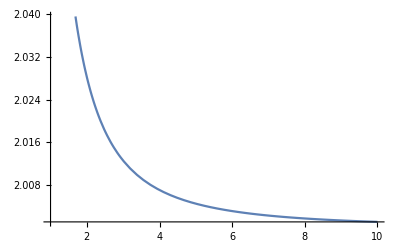

```mathematica
Plot[(1+2^(1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(-1+2 n)) (1+2^(-1-2 n) ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/n)^(1+2 n)),{n,1,10}]
```

```mathematica
(1+ ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/(2n))^(-1+2 n)) (1+ ((-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/(2n))^(1+2 n))>2
```

True

```mathematica
(1+ (K)^(-1+2 n)) (1+ (K)^(1+2 n))-2//Expand
```

-1+K^(4 n)+K^(-1+2 n)+K^(1+2 n)

```mathematica
(4 n^2)/(2n(√(4 n^2+Log[1+√2]^2)+Log[1+√2]))
```

```mathematica
FullSimplify[1/(Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2))==(-Log[1+√2]+√(4 n^2+Log[1+√2]^2))/(2n),n>0]
```

True

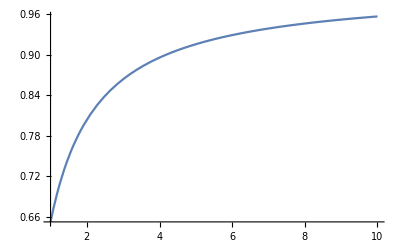

```mathematica
Plot[1/(Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)),{n,1,10}]
```

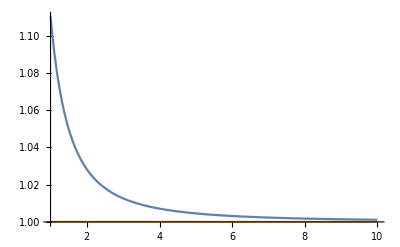

```mathematica
Plot[{(1/(Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)))^(4 n)+(1/(Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)))^(-1+2 n)+(1/(Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)))^(1+2 n),1},{n,1,10},PlotRange->All]
```

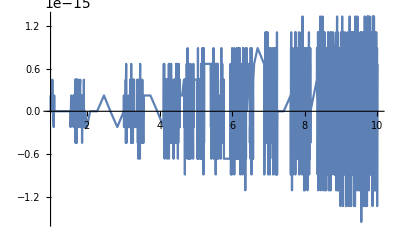

```mathematica
Plot[{(1/(Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)))^(4 n)+(1/(Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)))^(-1+2 n)+(1/(Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)))^(1+2 n)-(Exp[-4n Log[Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)]]+Exp[-(2n-1) Log[Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)]]+Exp[-(2n+1) Log[Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)]])},{n,1,10},PlotRange->All]
```

```mathematica
Exp[-4n Log[Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)]]+Exp[-(2n-1) Log[Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)]]+Exp[-(2n+1) Log[Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)]]>1
```

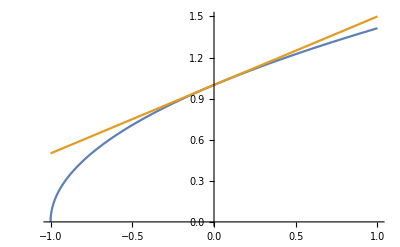

```mathematica
Plot[{√(1+x),1+x/2},{x,-1,1}]
```

```mathematica
Series[√(1+x),{x,0,4}]
```

1+x/2-x^2/8+x^3/16-(5 x^4)/128+O[x]^5

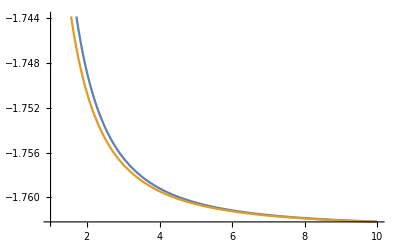

```mathematica
Plot[{-4n Log[Log[1+√2]/(2n)+√(1+(Log[1+√2]/(2n))^2)],-4n Log[1+Log[1+√2]/(2n)+1/2(Log[1+√2]/(2n))^2]},{n,1,10}]
```

### Enough:

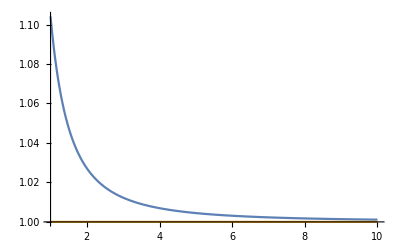

```mathematica
Plot[{Exp[-4n Log[1+Log[1+√2]/(2n)+1/2(Log[1+√2]/(2n))^2]]+Exp[-(2n-1) Log[1+Log[1+√2]/(2n)+1/2(Log[1+√2]/(2n))^2]]+Exp[-(2n+1) Log[1+Log[1+√2]/(2n)+1/2(Log[1+√2]/(2n))^2]],1},{n,1,10},PlotRange->All]
```

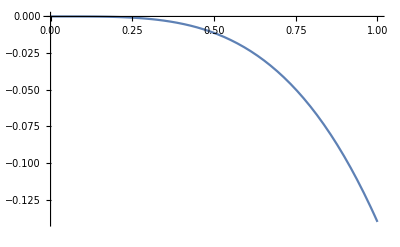

```mathematica
Plot[{Log[1+x]-(x-x^2/2+x^3/3)},{x,0,1}]
```

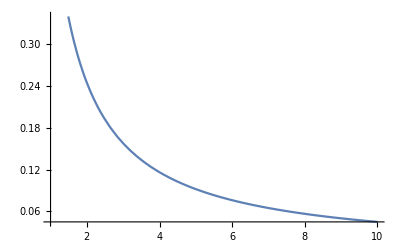

```mathematica
Plot[Log[1+√2]/(2n)+1/2(Log[1+√2]/(2n))^2,{n,1,10}]
```

### By using ln(1+x)≤x-x^2/2+x^3/3:

```mathematica
Log[1+Log[1+√2]/(2n)+1/2(Log[1+√2]/(2n))^2]/.Log[1+a_]->a-a^2/2+a^3/3
```

Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2)-1/2 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^2+1/3 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^3

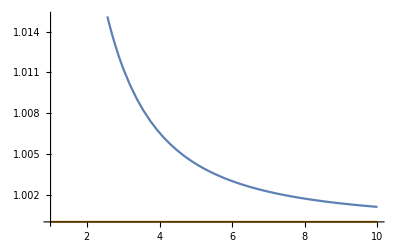

```mathematica
Plot[{Exp[-4n (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2)-1/2 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^2+1/3 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^3)]+Exp[-(2n-1) (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2)-1/2 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^2+1/3 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^3)]+Exp[-(2n+1) (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2)-1/2 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^2+1/3 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^3)],1},{n,1,10}]
```

```mathematica
Limit[Exp[-4n (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2)-1/2 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^2+1/3 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^3)]+Exp[-(2n-1) (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2)-1/2 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^2+1/3 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^3)]+Exp[-(2n+1) (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2)-1/2 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^2+1/3 (Log[1+√2]/(2 n)+Log[1+√2]^2/(8 n^2))^3)],n->∞]
```

1

### Enough:

```mathematica
Exp[-2 Log[1+√2]+Log[1+√2]^3/(12 n^2)-(3 Log[1+√2]^4)/(32 n^3)-Log[1+√2]^5/(32 n^4)-Log[1+√2]^6/(384 n^5)]+Exp[-Log[1+√2]+Log[1+√2]/(2 n)-Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)+(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)+Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)+Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5)]+Exp[-Log[1+√2]-Log[1+√2]/(2 n)+Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)-(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)-Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)-Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5)]>1
```

### That is

```mathematica
Plot[{(1/(1+√2)^2)Exp[Log[1+√2]^3/(12 n^2)-(3 Log[1+√2]^4)/(32 n^3)-Log[1+√2]^5/(32 n^4)-Log[1+√2]^6/(384 n^5)]+(-1+√2)Exp[Log[1+√2]/(2 n)-Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)+(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)+Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)+Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5)]+(-1+√2)Exp[-Log[1+√2]/(2 n)+Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)-(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)-Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)-Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5)],1},{n,1,10}]
```

-Graphics-

```mathematica
(1/(1+√2)^2)Exp[Log[1+√2]^3/(12 n^2)-(3 Log[1+√2]^4)/(32 n^3)-Log[1+√2]^5/(32 n^4)-Log[1+√2]^6/(384 n^5)]+(-1+√2)Exp[Log[1+√2]/(2 n)-Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)+(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)+Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)+Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5)]+(-1+√2)Exp[-Log[1+√2]/(2 n)+Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)-(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)-Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)-Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5)]
```

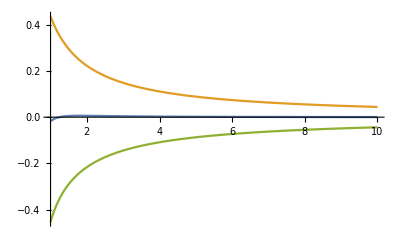

```mathematica
Plot[{Log[1+√2]^3/(12 n^2)-(3 Log[1+√2]^4)/(32 n^3)-Log[1+√2]^5/(32 n^4)-Log[1+√2]^6/(384 n^5),Log[1+√2]/(2 n)-Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)+(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)+Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)+Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5),-Log[1+√2]/(2 n)+Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)-(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)-Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)-Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5)},{n,1,10}]
```

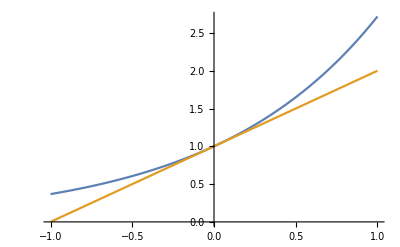

```mathematica
Plot[{Exp[x],1+x},{x,-1,1}]
```

```mathematica
(1/(1+√2)^2)Exp[Log[1+√2]^3/(12 n^2)-(3 Log[1+√2]^4)/(32 n^3)-Log[1+√2]^5/(32 n^4)-Log[1+√2]^6/(384 n^5)]+(-1+√2)Exp[Log[1+√2]/(2 n)-Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)+(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)+Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)+Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5)]+(-1+√2)Exp[-Log[1+√2]/(2 n)+Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)-(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)-Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)-Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5)]/.Exp[a_]->1+a
```

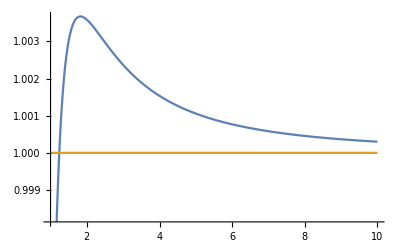

```mathematica
Plot[{(1+Log[1+√2]^3/(12 n^2)-(3 Log[1+√2]^4)/(32 n^3)-Log[1+√2]^5/(32 n^4)-Log[1+√2]^6/(384 n^5))/(1+√2)^2+(-1+√2) (1-Log[1+√2]/(2 n)+Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)-(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)-Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)-Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5))+(-1+√2) (1+Log[1+√2]/(2 n)-Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)+(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)+Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)+Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5)),1},{n,1,10}]
```

```mathematica
Simplify[(1+Log[1+√2]^3/(12 n^2)-(3 Log[1+√2]^4)/(32 n^3)-Log[1+√2]^5/(32 n^4)-Log[1+√2]^6/(384 n^5))/(1+√2)^2+(-1+√2) (1-Log[1+√2]/(2 n)+Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)-(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)-Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)-Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5))+(-1+√2) (1+Log[1+√2]/(2 n)-Log[1+√2]^3/(48 n^3)+Log[1+√2]^3/(24 n^2)+(3 Log[1+√2]^4)/(128 n^4)-(3 Log[1+√2]^4)/(64 n^3)+Log[1+√2]^5/(128 n^5)-Log[1+√2]^5/(64 n^4)+Log[1+√2]^6/(1536 n^6)-Log[1+√2]^6/(768 n^5))>1,n>0]
```

32 n^3>Log[1+√2] (6 n+Log[1+√2])^2

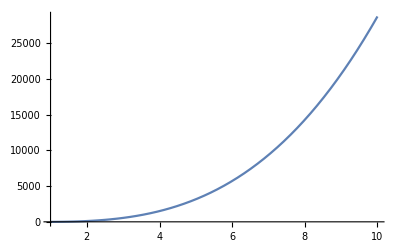

```mathematica
Plot[{32 n^3-Log[1+√2] (6 n+Log[1+√2])^2},{n,1,10}]
```

```mathematica
32 n^3-Log[1+√2] (6 n+Log[1+√2])^2//Expand
```

32 n^3-36 n^2 Log[1+√2]-12 n Log[1+√2]^2-Log[1+√2]^3

```mathematica
D[32 n^3-36 n^2 Log[1+√2]-12 n Log[1+√2]^2-Log[1+√2]^3,n]
```

96 n^2-72 n Log[1+√2]-12 Log[1+√2]^2